```mathematica
$HistoryLength=0;
```

## Initialization

```mathematica
projectDirectory="~/Documents/unireps";
```

```mathematica
datasetsDirectory=FileNameJoin[{projectDirectory,"datasets"}];
outputsDirectory=FileNameJoin[{projectDirectory,"outputs"}];
knnDirectory=FileNameJoin[{projectDirectory,"knn"}];
```

```mathematica
mxDir=FileNameJoin[{projectDirectory,"mx"}];
```

## Import k-NN

```mathematica
getDatasetName[{model_,dataset_,chat_:False}]:=
StringReplace[model,"/"->"__"]<>"---"<>dataset<>If[chat,"--chat",""]
```

```mathematica
getKNNDatasetPath[output_]:=
FileNameJoin[{knnDirectory,getDatasetName[output]}]
```

```mathematica
getKNNDataset[output_]:=Enclose@Import[ConfirmBy[getKNNDatasetPath[output],FileExistsQ],"Parquet"]
```

```mathematica
getKNN[output_,k_:10]:=
Enclose@With[{t=Confirm@getKNNDataset[output]},
Transpose[NumericArray[Normal@t[[All,"knn"]],"UnsignedInteger16"][[All,2;;,;;k]]]
]
```

## Mutual k-NN

```mathematica
mknn[knn1_,knn2_]:=Mean[N@MapThread[Length@*Intersection,{knn1,knn2}]]/Length[knn1[[1]]]
```

## Model list

```mathematica
allModels={
(*"openai-community/gpt2",*)
"google/gemma-2b",
"google/gemma-7b",
"google/gemma-2-2b",
"google/gemma-2-9b",
"google/gemma-2-9b-it",
"google/gemma-2-27b",
"meta-llama/Meta-Llama-3.1-8B",
"meta-llama/Meta-Llama-3.1-8B-Instruct",
"meta-llama/Llama-3.2-1B",
"meta-llama/Llama-3.2-3B",
"meta-llama/Llama-3.2-3B-Instruct",
"meta-llama/Llama-3.2-11B-Vision",
"meta-llama/Llama-3.1-70B",
"meta-llama/Llama-3.1-70B-Instruct",
"meta-llama/Llama-3.3-70B-Instruct",
"mistralai/Mistral-7B-v0.3",
"mistralai/Mistral-Nemo-Base-2407",
"mistralai/Mixtral-8x7B-v0.1",
"microsoft/Phi-3-mini-4k-instruct",
"microsoft/Phi-3-medium-4k-instruct",
"microsoft/Phi-3.5-mini-instruct",
"tiiuae/falcon-40b",
"tiiuae/falcon-11B",
"tiiuae/falcon-mamba-7b"
};
```

```mathematica
chatModels={
"google/gemma-2-9b-it",
"meta-llama/Meta-Llama-3.1-8B-Instruct",
"meta-llama/Llama-3.2-3B-Instruct",
"microsoft/Phi-3-mini-4k-instruct",
"microsoft/Phi-3-medium-4k-instruct",
"microsoft/Phi-3.5-mini-instruct",
"meta-llama/Llama-3.1-70B-Instruct",
"meta-llama/Llama-3.3-70B-Instruct"
};
```

```mathematica
allDatasets={
"web_text",
"web_text_caesar",
"imdb",
"random_strings",
"book_translations_en",
"book_translations_de",
"common_words",
"ifeval",
"mmlu"
};
```

```mathematica
modelDisplayNames=<|
"openai-community/gpt2"->"GPT-2",
"google/gemma-2b"->"Gemma (2B)",
"google/gemma-7b"->"Gemma (7B)",
"google/gemma-2-2b"->"Gemma 2 (2B)",
"google/gemma-2-9b"->"Gemma 2 (9B)",
"google/gemma-2-9b-it"->"Gemma 2 IT (9B)",
"google/gemma-2-27b"->"Gemma 2 (27B)",
"meta-llama/Meta-Llama-3.1-8B"->"Llama 3.1 (8B)",
"meta-llama/Meta-Llama-3.1-8B-Instruct"->"Llama 3.1 IT (8B)",
"meta-llama/Llama-3.2-1B"->"Llama 3.2 (1B)",
"meta-llama/Llama-3.2-3B"->"Llama 3.2 (3B)",
"meta-llama/Llama-3.2-3B-Instruct"->"Llama 3.2 IT (3B)",
"meta-llama/Llama-3.2-11B-Vision"->"Llama 3.2 Vision (11B)",
"meta-llama/Llama-3.1-70B"->"Llama 3.1 (70B)",
"meta-llama/Llama-3.1-70B-Instruct"->"Llama 3.1 IT (70B)",
"meta-llama/Llama-3.3-70B-Instruct"->"Llama 3.3 IT (70B)",
"mistralai/Mistral-7B-v0.3"->"Mistral v0.3 (7B)",
"mistralai/Mistral-Nemo-Base-2407"->"Mistral Nemo",
"mistralai/Mixtral-8x7B-v0.1"->"Mixtral v0.1 (8x7B)",
"microsoft/Phi-3-mini-4k-instruct"->"Phi 3 Mini IT",
"microsoft/Phi-3-medium-4k-instruct"->"Phi 3 Medium IT",
"microsoft/Phi-3.5-mini-instruct"->"Phi 3.5 Mini IT",
"tiiuae/falcon-40b"->"Falcon (40B)",
"tiiuae/falcon-11B"->"Falcon (11B)",
"tiiuae/falcon-mamba-7b"->"Falcon Mamba (7B)"
|>;
```

## Compute mutual k-NN matrices

```mathematica
LaunchKernels[];
allKNN=ParallelMap[
getKNN[{#,"web_text"}]&,
AssociationMap[Identity,allModels],
Method->"FinestGrained"
];//EchoTiming
CloseKernels[];
```

64.2931

```mathematica
LaunchKernels[];
allMKNN=ParallelMap[
Apply[Outer[mknn,Normal@allKNN@#1,Normal@allKNN@#2,1]&],
AssociationMap[Identity,DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort]],
Method->"FinestGrained"
];//EchoTiming
CloseKernels[];
```

125.033

```mathematica
lookupMKNN[mknns_,{m1_,m2_}]:=Lookup[mknns,Key[{m1,m2}],Transpose@Lookup[mknns,Key[{m2,m1}]]]
```

## Visualizations

```mathematica
infernoColors=With[{cs=},RGBColor@*First@*Nearest[Range[Length[cs]]/Length[cs]->cs]];
```

## Scratch space

### Tables

```mathematica
texts=Normal@getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","web_text"}][[All,"text"]];
```

```mathematica
t=1001;
```

```mathematica
nearestTexts=texts[[Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"},5][[10,t]]+1]];
```

```mathematica
formatTableText[t0_,l_:80]:=
With[{t=StringReplace[t0,"\n\n"->" "]},
StringTake[t,UpTo[l]]<>If[StringLength[t]>l,"...",""]]
```

```mathematica
CopyToClipboard[StringRiffle[
MapIndexed[
ToString@First@#2<>"&\\small\\texttt{"<>#1<>"}"&,
formatTableText/@nearestTexts
],
"\\\\\n"
]<>"\\\\\n"]
```

### Generalized diagonal

```mathematica
generalizedDiagonalMatrix[n_,m_]/;n>m:=Table[Boole[j<=i<=j+n-m],{i,n},{j,m}]
generalizedDiagonalMatrix[n_,m_]/;n<m:=Transpose@generalizedDiagonalMatrix[m,n]
generalizedDiagonalMatrix[n_,m_]/;n==m:=IdentityMatrix[n]
```

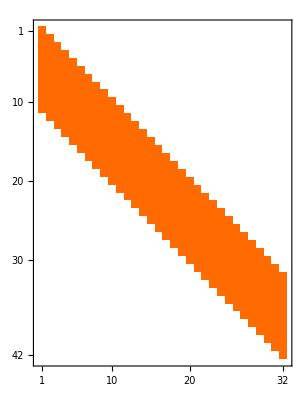

```mathematica
MatrixPlot[generalizedDiagonalMatrix@@Dimensions[mknn]]
```

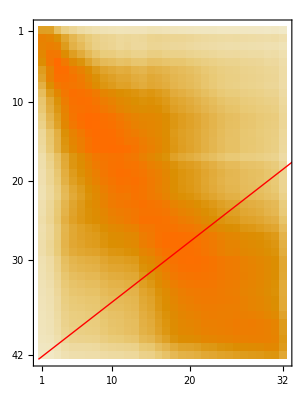

```mathematica
MatrixPlot[mknn,Epilog->{Red,Line[{{0,0},Dimensions[mknn]}]}]
```

```mathematica
onOffDiagonalMean[mknn_]:=With[{mask=generalizedDiagonalMatrix@@Dimensions[mknn]},
{Total[mknn*mask,2]/Total[mask,2],Total[mknn*(1-mask),2]/Total[(1-mask),2]}
]
```

```mathematica
onOffDiagonalMean@mknn
```

{0.465313,0.296484}

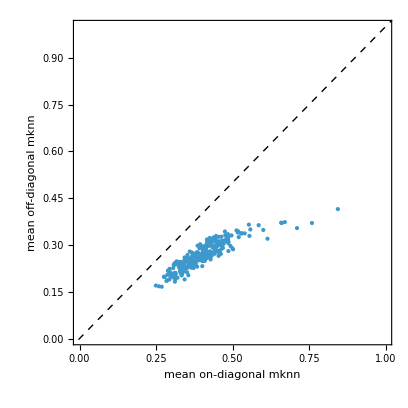

```mathematica
ListPlot[
onOffDiagonalMean[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
PlotRange->{{0,1},{0,1}},
Frame->{{True,False},{True,False}},
FrameLabel->{"mean on-diagonal mknn","mean off-diagonal mknn"}
]
```

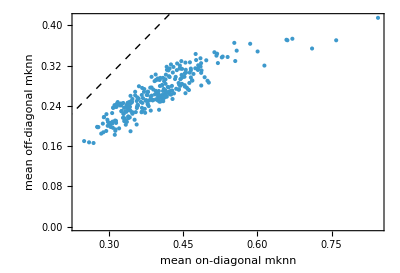

```mathematica
ListPlot[
onOffDiagonalMean[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
(*PlotRange->{{0,1},{0,1}},*)
PlotRange->All,
Frame->{{True,False},{True,False}},
FrameLabel->{"mean on-diagonal mknn","mean off-diagonal mknn"}
]
```

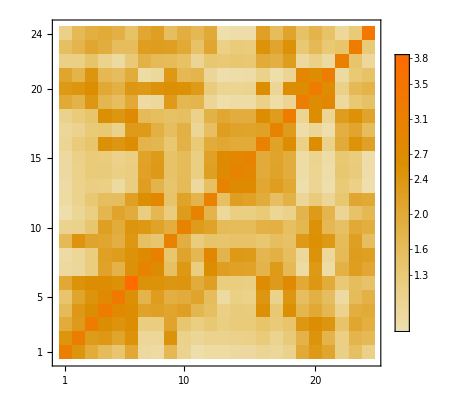

```mathematica
MatrixPlot[
Table[Divide@@onOffDiagonalMean@lookupMKNN[allMKNN,{m1,m2}],{m1,Keys@allKNN},{m2,Keys@allKNN}],
DataReversed->True,
PlotLegends->True
]
```

```mathematica
onOffDiagonalValues[mknn_]:=With[{mask=generalizedDiagonalMatrix@@Dimensions[mknn]},
{Catenate@MapThread[Pick[#1,#2,1]&,{mknn,mask}],Catenate@MapThread[Pick[#1,#2,1]&,{mknn,1-mask}]}
]
```

```mathematica
onOffDiagonalMean[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ]==(Mean/@onOffDiagonalValues[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ])
```

True

```mathematica
onOffVals=onOffDiagonalValues[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ];
```

```mathematica
pvalues=TTest[#,VerifyTestAssumptions->None]&/@onOffVals;
```

General::munfl: 3.06647688313060394363632×10^-339 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.99952455418391103325231×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.54679178912259555613399×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
pvaluesOneTailed=TTest[#,AlternativeHypothesis->"Greater",VerifyTestAssumptions->None]&/@onOffVals;
```

General::munfl: 3.06647688313060394363632×10^-339 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.99952455418391103325231×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.54679178912259555613399×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MinMax[Subtract@@@Map[Mean,onOffVals,{2}]]
```

{0.069517,0.429078}

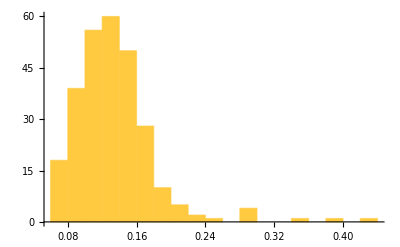

```mathematica
Histogram[Subtract@@@Map[Mean,onOffVals,{2}],PlotRange->All]
```

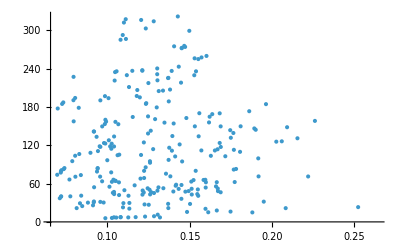

```mathematica
ListPlot[Transpose[{
Subtract@@@Map[Mean,onOffVals,{2}],
-Log10[pvalues]
}]]
```

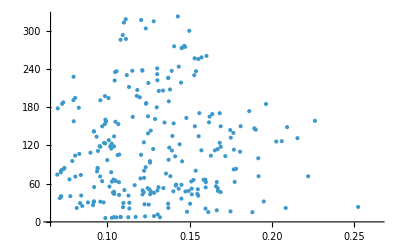

```mathematica
ListPlot[Transpose[{
Subtract@@@Map[Mean,onOffVals,{2}],
-Log10[pvaluesOneTailed]
}]]
```

### Monotonic random walks

```mathematica
mknn=lookupMKNN[allMKNN,{"google/gemma-2-9b","meta-llama/Meta-Llama-3.1-8B"}];
mknn=If[Dimensions[mknn][[1]]<Dimensions[mknn][[2]],Transpose[mknn],mknn];
```

```mathematica
dists=Normalize[#,Total]&/@mknn;
```

```mathematica
monotonicProb[dists_]:=Total[Fold[Accumulate[#1*#2]&,1,Most@dists]*Last[dists]]
```

```mathematica
Sum[dists[[1,i]]*dists[[2,j]]*dists[[3,k]],{i,1,Length[dists[[1]]]},{j,1,i},{k,1,j}]
```

0.184709

```mathematica
Count[Transpose[{
RandomChoice[dists[[1]]->Range[Length[dists[[1]]]],1000000],
RandomChoice[dists[[2]]->Range[Length[dists[[1]]]],1000000],
RandomChoice[dists[[3]]->Range[Length[dists[[1]]]],1000000]
}],{a_,b_,c_}/;a<=b<=c]/1000000//N
```

0.183466

```mathematica
monotonicProb@dists[[;;3]]
```

0.183802

```mathematica
Count[
Transpose@Table[RandomChoice[dists[[i]]->Range[Length[dists[[i]]]],1000000],{i,7}],
l_List/;LessEqual@@l
]/1000000//N
```

0.000458

```mathematica
monotonicProb@dists[[;;7]]
```

0.000398761

```mathematica
monotonicProb@dists
```

7.31329×10^-37

```mathematica
sumNestedTriangularSum2@Log@dists[[;;3]]
```

-63115.3

```mathematica
monotonicProb@ConstantArray[N@1/Dimensions[dists][[2]],Dimensions[dists]]
```

2.35136×10^-43

```mathematica
monotonicProb@dists
```

7.31329×10^-37

```mathematica
monotonicness[mknn_]:=
Module[{dists,nullDists},
dists=Normalize[#,Total]&/@mknn;
nullDists=ConstantArray[N@1/Dimensions[dists][[2]],Dimensions[dists]];
monotonicProb[dists]/monotonicProb[nullDists]
]
```

```mathematica
Log@monotonicness[mknn]
```

14.9502

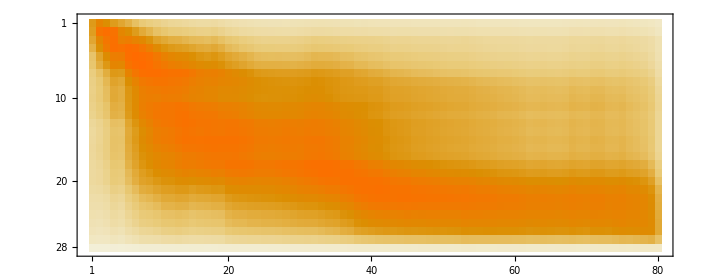

```mathematica
MatrixPlot@lookupMKNN[allMKNN,{"google/gemma-7b","meta-llama/Llama-3.1-70B"}]
```

```mathematica
monotonicness@lookupMKNN[allMKNN,{"meta-llama/Llama-3.1-70B","google/gemma-7b"}]
```

7.26578×10^10

```mathematica
bFactors=Table[monotonicness@lookupMKNN[allMKNN,{m1,m2}],{m1,Keys@allKNN},{m2,Keys@allKNN}];
```

```mathematica
MinMax@bFactors
```

{45.4589,8.04841×10^22}

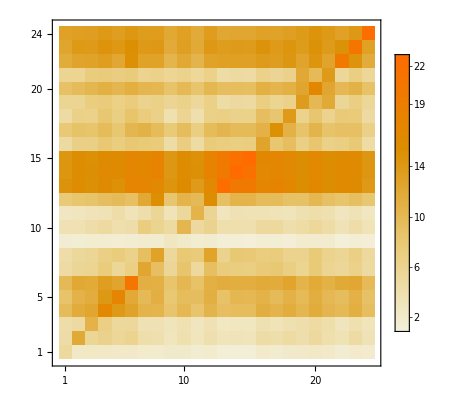

```mathematica
MatrixPlot[
Table[Log10@monotonicness@lookupMKNN[allMKNN,{m1,m2}],{m1,Keys@allKNN},{m2,Keys@allKNN}],
DataReversed->True,
PlotLegends->Automatic
]
```

### Max similarity plots

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,Keys@allKNN},{m2,DeleteCases[Keys@allKNN,m1]}
];
```

```mathematica
mknnPaths=Map[
mat|->MapIndexed[N@{First[#2],Ordering[#1,-1][[1]]}/Dimensions[mat]&,mat],
mknnMats
];
```

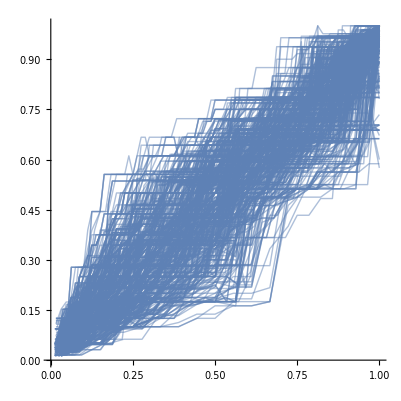

```mathematica
ListLinePlot[
mknnPaths,
PlotStyle->Directive[Opacity[0.5],Thin,ColorData[97][1]],
AspectRatio->1,
PlotRange->{{0,1},{0,1}}
]
```

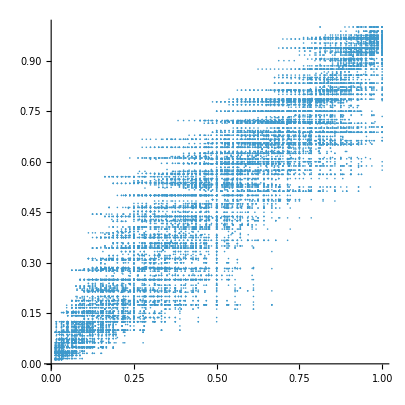

```mathematica
ListPlot[
Catenate@mknnPaths,
AspectRatio->1,
PlotRange->{{0,1},{0,1}}
]
```

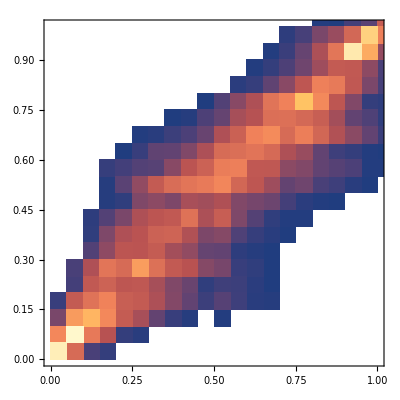

```mathematica
DensityHistogram[Catenate@mknnPaths,PlotRange->{{0,1},{0,1}}]
```

### Aggregate plots

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,Keys@allKNN},{m2,DeleteCases[Keys@allKNN,m1]}
];
```

```mathematica
pointValues=Catenate@Map[
mat|->Catenate@MapIndexed[N@#2/Dimensions[mat]->#1&,mat,{2}],
mknnMats
];
```

```mathematica
mat=Map[Mean,BinLists[pointValues,1/45,1/45],{2}];
```

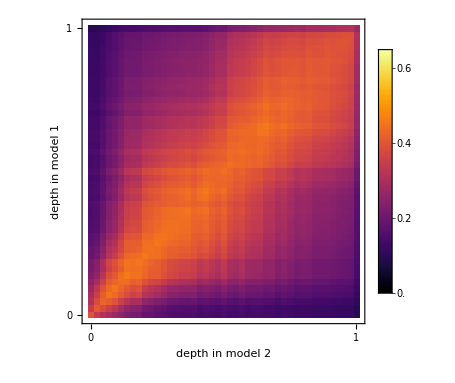

```mathematica
ArrayPlot[
Reverse@mat,
DataReversed->False,
DataRange->{{0,1},{0,1}},
ColorFunction->(infernoColors[#/0.65]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,0.65}}],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->All,
FrameLabel->{"depth in model 1","depth in model 2"}
]
```

### Square big mats

```mathematica
imgs=Table[
Image[Map[infernoColors,Reverse@lookupMKNN[allMKNN,{m1,m2}],{2}]],
{m1,Keys@allKNN},{m2,Keys@allKNN}
];
```

```mathematica
imgSize=100;
```

```mathematica
i=ImageAssemble@Reverse@Map[ImageResize[#,{imgSize,imgSize},Resampling->"Nearest"]&,imgs,{2}];
```

```mathematica
horizTicks=MapIndexed[
{First[#2]*imgSize-imgSize/2,modelDisplayNames@#1,{0,0.01}}&,
Keys@allKNN
];
vertTicks=MapIndexed[
{First[#2]*imgSize-imgSize/2,Rotate[modelDisplayNames@#1,Pi/2],{0,0.01}}&,
Keys@allKNN
];
```

```mathematica
Legended[
Graphics[
i,
PlotRangePadding->None,
Frame->{{True,False},{False,True}},
FrameTicks->{{horizTicks,horizTicks},{vertTicks,vertTicks}}
],
BarLegend[{infernoColors,{0,1}}]
]
```

-Graphics-

### Big mats

```mathematica
mat=ArrayFlatten@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,allModels},{m2,allModels}
];
```

```mathematica
modelLayers=Length/@allKNN;
modelPositions=Prepend[Accumulate[Lookup[modelLayers,Keys@allKNN]],0];
horizTicks=MapThread[
{#1,modelDisplayNames@#2,{0,0.01}}&,
{Mean[{Most@modelPositions,Rest@modelPositions}],allModels}
];
vertTicks=MapThread[
{#1,Rotate[modelDisplayNames@#2,Pi/2],{0,0.01}}&,
{Mean[{Most@modelPositions,Rest@modelPositions}],allModels}
];
ArrayPlot[
mat,
DataReversed->True,
(*ColorFunction->"SunsetColors",*)
(*ColorFunction->(Blend[RGBColor/@,#]&),*)
ColorFunction->infernoColors,
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,1}}],
PlotRangePadding->None,
Frame->{{True,False},{False,True}},
FrameTicks->{{horizTicks,horizTicks},{vertTicks,vertTicks}}(*,
GridLines->{modelPositions,modelPositions},
GridLinesStyle->Directive[Green,Opacity[1]]*)
]
```

-Graphics-

### Other

```mathematica
Do[getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","web_text"}];Echo[MemoryInUse[]],10];
```

```mathematica
t=getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","web_text"}]
```

```mathematica
MemoryInUse[]
```

839216648

```mathematica
Clear[t]
```

```mathematica
na=getKNN[{"google/gemma-2-9b","web_text"},10]//EchoTiming
```

6.11261

NumericArray[<42,2048,10>, UnsignedInteger16]

```mathematica
na=getKNN[{"mistralai/Mistral-7B-v0.3","web_text"},10]//EchoTiming
```

4.62147

NumericArray[<32,2048,10>, UnsignedInteger16]

```mathematica
na2=getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"},10]//EchoTiming
```

4.63855

NumericArray[<32,2048,10>, UnsignedInteger16]

```mathematica
na2=getKNN[{"meta-llama/Llama-3.1-70B-Instruct","web_text"},10]//EchoTiming
```

11.7751

NumericArray[<80,2048,10>, UnsignedInteger16]

```mathematica
mknn[knn1_,knn2_]:=Mean[N@MapThread[Length@*Intersection,{knn1,knn2}]]/Length[knn1[[1]]]
```

```mathematica
mat=Outer[mknn,Normal@na,Normal@na2,1];//EchoTiming
```

4.72297

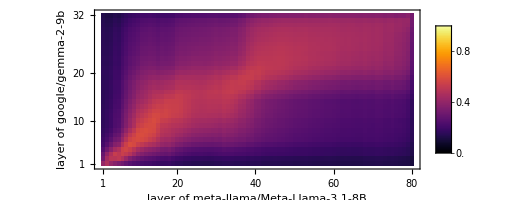

```mathematica
MatrixPlot[
mat,
DataReversed->True,
(*ColorFunction->(ColorData["SunsetColors"][#]&),*)
ColorFunction->(Blend[RGBColor/@,#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,1}}],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->Replace[AbsoluteOptions[MatrixPlot[mat,DataReversed->True,PlotRangePadding->None],FrameTicks][[1,2]],{a_,b_}:>{a+1/2,b,{0,0.01}},{3}],
FrameLabel->{"layer of google/gemma-2-9b","layer of meta-llama/Meta-Llama-3.1-8B"}
]
```

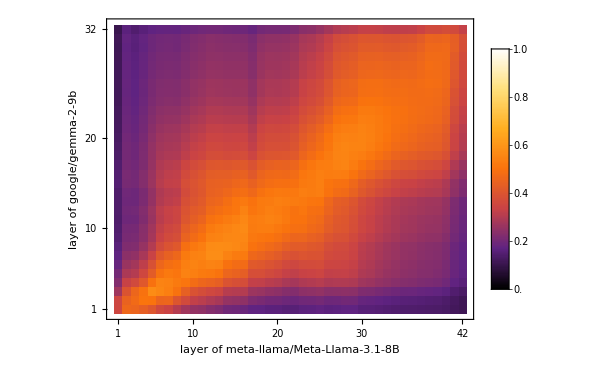

```mathematica
MatrixPlot[
mat,
DataReversed->True,
ColorFunction->(ColorData["SunsetColors"][#]&),
(*ColorFunction->(Blend[RGBColor/@,#]&),*)
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,1}}],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->Replace[AbsoluteOptions[MatrixPlot[mat,DataReversed->True,PlotRangePadding->None],FrameTicks][[1,2]],{a_,b_}:>{a+1/2,b,{0,0.01}},{3}],
FrameLabel->{"layer of google/gemma-2-9b","layer of meta-llama/Meta-Llama-3.1-8B"}
]
```

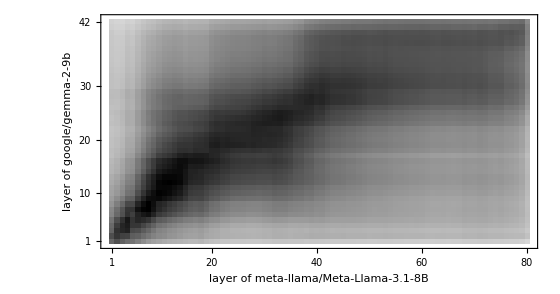

```mathematica
MatrixPlot[
mat,
DataReversed->True,
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,1}}],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->Replace[AbsoluteOptions[MatrixPlot[mat,DataReversed->True,PlotRangePadding->None],FrameTicks][[1,2]],{a_,b_}:>{a+1/2,b,{0,0.01}},{3}],
FrameLabel->{"layer of google/gemma-2-9b","layer of meta-llama/Meta-Llama-3.1-8B"}
]
```

```mathematica
mknn[Normal@na[[5]],Normal@na[[10]]]
```

```mathematica
mknn[Normal@na[[5]],Normal@na[[10]]]
```

```mathematica
mknn[Normal@na[[5]],Normal@na[[10]]]
```

0.398975

```mathematica
na
```

NumericArray[<33,2048,10>, UnsignedInteger16]

```mathematica
ByteCount[na]
```

276689056

```mathematica
ByteCount[t]
```

284471207